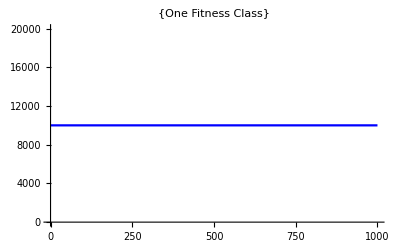

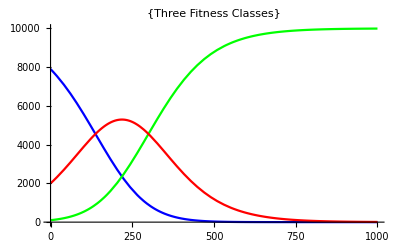

```mathematica
(* Testing SystemSolver, SolveDiffEqs *)
Δc1=0.01;
Δc2=0.02;
popsize=10^4;
timestep=1000; 
(* Testing system solver for one fitness class *)
genotypes={{1,1}};
genotypeabundances={10^4};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue},PlotLabel->{"One Fitness Class"}]
(* Testing system solver for three fitness class *)
genotypes={{1,1},{1,2},{2,1}};
genotypeabundances={10^4-100-2000,100,2000};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]],n2[t]/.sol[[1]],n3[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue,Green,Red},PlotLabel->{"Three Fitness Classes"}]
```

```mathematica
(* Testing module that checks for new mutations, NextMutation *)
Δc1=0.01;
Δc2=0.02;
U1=2 10^-4;
U2=1 10^-4;
popsize=10^6;
starttime=0;
timestep=100; 
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

```mathematica
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
```

```mathematica
getNextMutants[genotypes]
NextMutation[popsize,Δc1,Δc2,U1,U2,sol,genotypes,starttime,timestep]
```

{{{4,1},{{6,1}},0,0},{{3,2},{{5,1},{6,2}},0,0},{{2,3},{{3,1},{5,2}},0,0},{{1,4},{{3,2}},0,0}}

{30.9401,{{1,4}},True,0.0393006,{{3,2}}}

```mathematica
(* simulation parameters *)
Δc1=0.01;
Δc2=0.02;
U1=2 10^-4;
U2=0 10^-4;
popsize=10^6;
starttime=0;
timestep=1000; 
maxtime=50000;
fulldata=0;
verbose=False;
veryverbose=False;
(* Check Regimes *)
Print["Trait 1 q = ",If[U1==0,0,2 Log[popsize Δc1]/Log[Δc1/U1]]," in ", If[U1==0," No Evolution Regime ",If[2 Log[popsize Δc1]/Log[Δc1/U1]< 2,"Successional Regime","Concurrent Mutations Regime"]], " with expected time scale ",If[U1==0,0,((Δc1(2 Log[popsize Δc1]-Log[Δc1/U1]))/Log[Δc1/U1]^2)^-1]];
Print["Trait 2 q = ",If[ U2==0,0,2 Log[popsize Δc2]/Log[Δc2/U2]]," in ", If[U2==0,"No Evolution Regime",If[2 Log[popsize Δc2]/Log[Δc2/U2]< 2,"Successional Regime","Concurrent Mutations Regime"]]," with expected time scale ",If[U2==0,0,((Δc2(2 Log[popsize Δc2]-Log[Δc2/U2]))/Log[Δc2/U2]^2)^-1]];(* Testing one trait evolution *)
r=0.5;
genotypes={{1,1},{2,1},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481

Trait 2 q = 0 in No Evolution Regime with expected time scale 0

mean substitutional load = 0.0346001

mean q = 3.46001

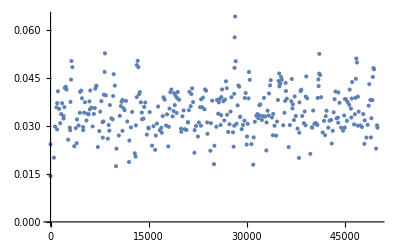

```mathematica
(* Run simulation *)
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
meansubload1=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitutional load = ",meansubload1];
Print["mean q = ",meansubload1/Δc1];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads]
```

```mathematica
(* simulation parameters *)
Δc1=0.01;
Δc2=0.02;
U1=0 10^-4;
U2=1 10^-4;
popsize=10^6;
starttime=0;
timestep=1000; 
maxtime=50000;
fulldata=0;
verbose=False;
veryverbose=False;
(* Check Regimes *)
Print["Trait 1 q = ",If[U1==0,0,2 Log[popsize Δc1]/Log[Δc1/U1]]," in ", If[U1==0," No Evolution Regime ",If[2 Log[popsize Δc1]/Log[Δc1/U1]< 2,"Successional Regime","Concurrent Mutations Regime"]], " with expected time scale ",If[U1==0,0,((Δc1(2 Log[popsize Δc1]-Log[Δc1/U1]))/Log[Δc1/U1]^2)^-1]];
Print["Trait 2 q = ",If[ U2==0,0,2 Log[popsize Δc2]/Log[Δc2/U2]]," in ", If[U2==0,"No Evolution Regime",If[2 Log[popsize Δc2]/Log[Δc2/U2]< 2,"Successional Regime","Concurrent Mutations Regime"]]," with expected time scale ",If[U2==0,0,((Δc2(2 Log[popsize Δc2]-Log[Δc2/U2]))/Log[Δc2/U2]^2)^-1]];(* Testing one trait evolution *)
r=0.5;
genotypes={{1,1},{1,2},{1,3}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 0 in  No Evolution Regime  with expected time scale 0

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428

mean substitutional load = 0.0597324

mean q = 2.98662

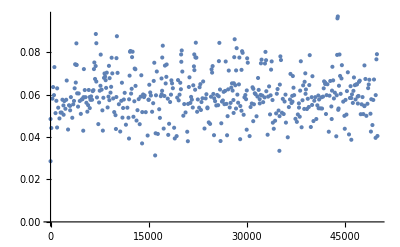

```mathematica
(* Run simulation *)
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
meansubload2=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitutional load = ",meansubload2];
Print["mean q = ",meansubload2/Δc2];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads]
```

```mathematica
(* simulation parameters *)
Δc1=0.01;
Δc2=0.02;
U1=2 10^-4;
U2=1 10^-4;
popsize=10^6;
starttime=0;
timestep=1000; 
maxtime=20000;
fulldata=0;
verbose=False;
veryverbose=False;
(* Check Regimes *)
Print["Trait 1 q = ",If[U1==0,0,2 Log[popsize Δc1]/Log[Δc1/U1]]," in ", If[U1==0," No Evolution Regime ",If[2 Log[popsize Δc1]/Log[Δc1/U1]< 2,"Successional Regime","Concurrent Mutations Regime"]], " with expected time scale ",If[U1==0,0,((Δc1(2 Log[popsize Δc1]-Log[Δc1/U1]))/Log[Δc1/U1]^2)^-1]];
Print["Trait 2 q = ",If[ U2==0,0,2 Log[popsize Δc2]/Log[Δc2/U2]]," in ", If[U2==0,"No Evolution Regime",If[2 Log[popsize Δc2]/Log[Δc2/U2]< 2,"Successional Regime","Concurrent Mutations Regime"]]," with expected time scale ",If[U2==0,0,((Δc2(2 Log[popsize Δc2]-Log[Δc2/U2]))/Log[Δc2/U2]^2)^-1]];
(* Testing two trait evolution *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428

mean substitution load = 0.0573014

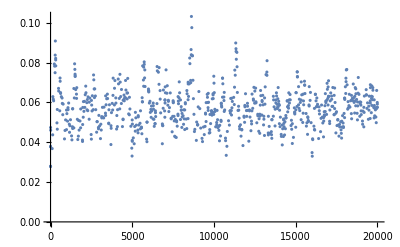

```mathematica
(* Run simulation *)
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
meansubload=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitution load = ",meansubload];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads]
```

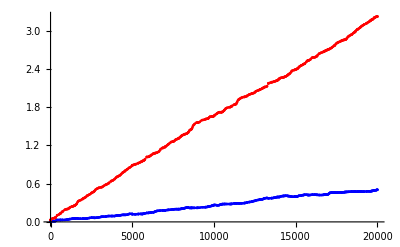

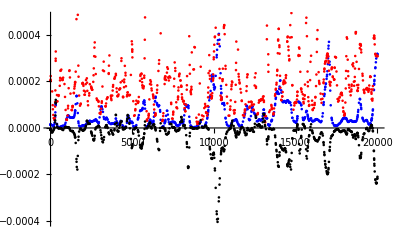

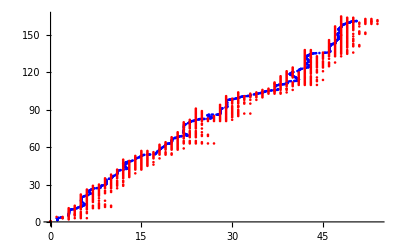

```mathematica
timesAndMean1=Table[{results[[i]][[1]],results[[i]][[2]]},{i,1,Length[results]}];
timesAndMean2=Table[{results[[i]][[1]],results[[i]][[3]]},{i,1,Length[results]}];
timesAndVar1=Table[{results[[i]][[1]],results[[i]][[6]]},{i,1,Length[results]}];
timesAndVar2=Table[{results[[i]][[1]],results[[i]][[7]]},{i,1,Length[results]}];
timesAndCov=Table[{results[[i]][[1]],results[[i]][[5]]},{i,1,Length[results]}];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
ListPlot[{timesAndMean1,timesAndMean2},PlotStyle->{Blue,Red}]
ListPlot[{timesAndVar1,timesAndVar2,timesAndCov},PlotStyle->{Blue,Red,Black}]
ListPlot[{mean2mean,noseTravel},PlotStyle->{Blue,Red}]
```

```mathematica
plots=Table[ListPlot[{mean2mean[[1;;i]],noseTravel[[1;;i]]},PlotStyle->{Black,Red},PlotRange->{{0,60},{0,150}}],{i,1,Length[mean2mean]}];
```

```mathematica
Export["~/twoDgrowth.avi",plots]
```

~/twoDgrowth.avi

```mathematica
(* simulation parameters *)
Δc1=0.01;
Δc2=0.02;
U1=2 10^-4;
U2=1 10^-4;
popsize=10^6;
starttime=0;
timestep=1000; 
maxtime=20000;
fulldata=1;
verbose=False;
veryverbose=False;
(* Check Regimes *)
Print["Trait 1 q = ",If[U1==0,0,2 Log[popsize Δc1]/Log[Δc1/U1]]," in ", If[U1==0," No Evolution Regime ",If[2 Log[popsize Δc1]/Log[Δc1/U1]< 2,"Successional Regime","Concurrent Mutations Regime"]], " with expected time scale ",If[U1==0,0,((Δc1(2 Log[popsize Δc1]-Log[Δc1/U1]))/Log[Δc1/U1]^2)^-1]];
Print["Trait 2 q = ",If[ U2==0,0,2 Log[popsize Δc2]/Log[Δc2/U2]]," in ", If[U2==0,"No Evolution Regime",If[2 Log[popsize Δc2]/Log[Δc2/U2]< 2,"Successional Regime","Concurrent Mutations Regime"]]," with expected time scale ",If[U2==0,0,((Δc2(2 Log[popsize Δc2]-Log[Δc2/U2]))/Log[Δc2/U2]^2)^-1]];
(* Testing two trait evolution *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428

```mathematica
(* Run simulation *)
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
```

```mathematica
(* Analyze behavior of blob *)
blob=results[[;;,{2,4,5}]];
```

```mathematica
Do[
Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
```

```mathematica
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large}],{i,1,Length[blob]}];
Export["~/travelingblob.avi",plots];
```